```mathematica
fp[θ_,ϕ_]:=(1/4)(Sin[θ]^2)((1+Cos[ϕ])^2);
fe[θ_,ϕ_]:=(1/4)(Sin[θ])((1+Cos[ϕ])^2);
fp[θ,ϕ]
fe[θ,ϕ]
SphericalPlot3D[fp[θ,ϕ],{θ,-4 π,2 π},{ϕ,-2 π,2 π},PlotTheme->"Detailed",PlotStyle->RGBColor[0.91,0.61,1.],PlotPoints->50,PlotRange->All]
SphericalPlot3D[fe[θ,ϕ],{θ,-4 π,2 π},{ϕ,-2 π,2 π},PlotTheme->"Detailed",PlotPoints->50,PlotRange->All]
```

1/4 (1+Cos[ϕ])^2 Sin[θ]^2

1/4 (1+Cos[ϕ])^2 Sin[θ]

-Graphics3D-

-Graphics3D-

Sin[θ]^2

Sin[θ]

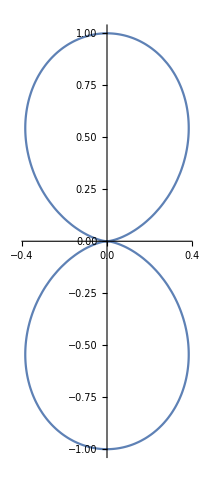

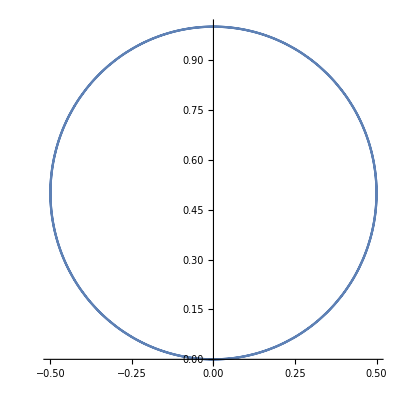

```mathematica
(*Los valores comentados son igual a Cero*)
fp[θ,0]
(*fp[0,ϕ]*)
fe[θ,0]
(*fe[0,ϕ]*)
(*Las graficas Son*)
PolarPlot[fp[θ,0],{θ,0,2 π}]
(*PolarPlot[fp[0,ϕ],{ϕ,0,2 π}]*)
PolarPlot[fe[θ,0],{θ,0,2 π}]
(*PolarPlot[fe[0,ϕ],{ϕ,0,2 π}]*)
```

Sin[θ]^2/4

1/4 (1+Cos[ϕ])^2

Sin[θ]/4

1/4 (1+Cos[ϕ])^2

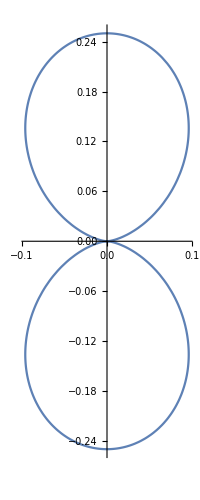

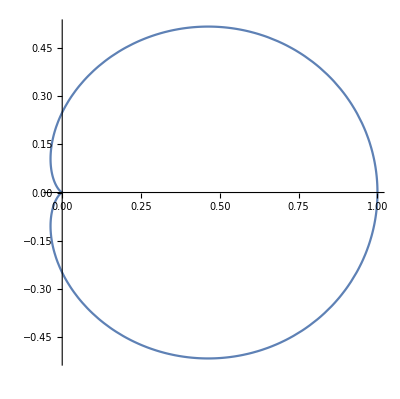

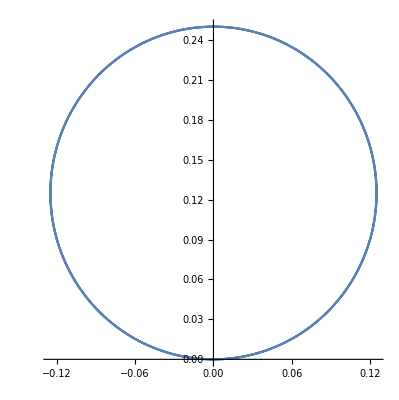

-Graphics-

```mathematica
fp[θ,Pi/2]
fp[Pi/2,ϕ]
fe[θ,Pi/2]
fe[Pi/2,ϕ]
(*Las graficas Son*)
PolarPlot[fp[θ,Pi/2],{θ,0,2 π}]
PolarPlot[fp[Pi/2,ϕ],{ϕ,0,2 π}]
PolarPlot[fe[θ,Pi/2],{θ,0,2 π}]
PolarPlot[fe[Pi/2,ϕ],{ϕ,0,2 π}]
```

Sin[θ]^2/4

1/4 (1+Cos[ϕ])^2

Sin[θ]/4

-1/4 (1+Cos[ϕ])^2

-Graphics-

-Graphics-

-Graphics-

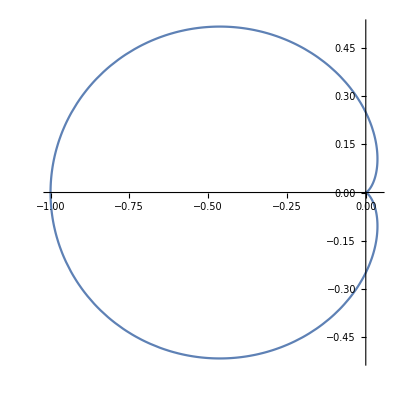

```mathematica
fp[θ,3Pi/2]
fp[3Pi/2,ϕ]
fe[θ,3Pi/2]
fe[3Pi/2,ϕ]
(*Las graficas Son*)
PolarPlot[fp[θ,3Pi/2],{θ,0,2 π}]
PolarPlot[fp[3Pi/2,ϕ],{ϕ,0,2 π}]
PolarPlot[fe[θ,3Pi/2],{θ,0,2 π}]
PolarPlot[fe[3Pi/2,ϕ],{ϕ,0,2 π}]
```